ⅇ^(-x^2-y^2)-2 ⅇ^(-x^2-y^2) x^2

-2 ⅇ^(-x^2-y^2) x y

-Graphics-

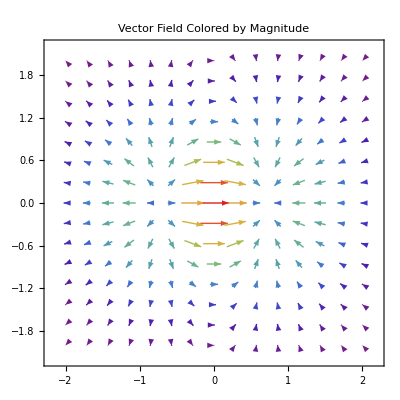

```mathematica
f[x_,y_]:=x Exp[-(x^2+y^2)];
A[x_,y_]=D[f[x,y],x]
B[x_,y_]=D[f[x,y],y]
ContourPlot[f[x,y],{x,-2,2},{y,-2,2},PlotPoints->100,Contours->30,ContourStyle->None,PlotLegends->Automatic,ColorFunction->"Rainbow"]
VectorPlot[{A[x,y],B[x,y]},{x,-2,2},{y,-2,2},VectorColorFunction->Function[{x,y,u,v,norm},ColorData["Rainbow"][norm]],VectorColorFunctionScaling->True,PlotLabel->"Vector Field Colored by Magnitude"]
```

```mathematica
f[x_,y_]:=x Exp[-(x^2+y^2)];
grad=Grad[f[x,y],{x,y}]
plot1=ContourPlot[f[x,y],{x,-2,2},{y,-2,2},PlotPoints->100,Contours->30,ContourStyle->None,PlotLegends->Automatic];
plot2=VectorPlot[grad,{x,-2,2},{y,-2,2},VectorStyle->Black];
Show[plot1,plot2]
```

{ⅇ^(-x^2-y^2)-2 ⅇ^(-x^2-y^2) x^2,-2 ⅇ^(-x^2-y^2) x y}

-Graphics-

```mathematica
f[x_,y_]:=x Exp[-(x^2+y^2)];
A=D[f[x,y],x]
B=D[f[x,y],y]
plot1=ContourPlot[f[x,y],{x,-2,2},{y,-2,2},PlotPoints->100,Contours->30,ContourStyle->None,PlotLegends->BarLegend[{"TemperatureMap",{-5,5}}],ColorFunction->"TemperatureMap"];
plot2=VectorPlot[{A,B},{x,-2,2},{y,-2,2},VectorStyle->Black];
Show[plot1,plot2]
```

ⅇ^(-x^2-y^2)-2 ⅇ^(-x^2-y^2) x^2

-2 ⅇ^(-x^2-y^2) x y

-Graphics-

```mathematica
f[x_,y_]:=x Exp[-(x^2+y^2)];
A=D[f[x,y],x]
B=D[f[x,y],y]
plot1=ContourPlot[f[x,y],{x,-2,2},{y,-2,2},PlotPoints->100,Contours->30,ContourStyle->None,PlotLegends->BarLegend[{"TemperatureMap",{0,1}}],ColorFunction->"TemperatureMap"];
plot2=VectorPlot[{A,B},{x,-2,2},{y,-2,2},VectorStyle->Black];
Show[plot1,plot2]
```

ⅇ^(-x^2-y^2)-2 ⅇ^(-x^2-y^2) x^2

-2 ⅇ^(-x^2-y^2) x y

-Graphics-

```mathematica
f[x_,y_]:=x Exp[-(x^2+y^2)];
A=D[f[x,y],x]
B=D[f[x,y],y]
plot1=ContourPlot[f[x,y],{x,-2,2},{y,-2,2},PlotPoints->100,Contours->30,ContourStyle->None,ContourLabels->True,PlotLegends->BarLegend[{"TemperatureMap",{0,1}}],(*Setting range in legend may show wrong data from the plot*)ColorFunction->"TemperatureMap"];
plot2=VectorPlot[{A,B},{x,-2,2},{y,-2,2},VectorStyle->Black];
Show[plot1,plot2]
```

ⅇ^(-x^2-y^2)-2 ⅇ^(-x^2-y^2) x^2

-2 ⅇ^(-x^2-y^2) x y

-Graphics-

```mathematica
f[x_,y_]:=x Exp[-(x^2+y^2)];
A=D[f[x,y],x]
B=D[f[x,y],y]
plot1=ContourPlot[f[x,y],{x,-2,2},{y,-2,2},PlotPoints->100,Contours->30,ContourStyle->None,PlotLegends->BarLegend[Automatic,None],ColorFunction->"TemperatureMap"];
plot2=VectorPlot[{A,B},{x,-2,2},{y,-2,2},VectorStyle->Black];
Show[plot1,plot2]
```

ⅇ^(-x^2-y^2)-2 ⅇ^(-x^2-y^2) x^2

-2 ⅇ^(-x^2-y^2) x y

-Graphics-

```mathematica
f[x_,y_]:=x Exp[-(x^2+y^2)];
grad=Grad[f[x,y],{x,y}]
plot1=ContourPlot[f[x,y],{x,-2,2},{y,-2,2},PlotPoints->100,Contours->30,ContourStyle->None,PlotLegends->Automatic,ColorFunction->"TemperatureMap"];
plot2=VectorPlot[grad,{x,-2,2},{y,-2,2},VectorStyle->Black];
Show[plot1,plot2]
```

{ⅇ^(-x^2-y^2)-2 ⅇ^(-x^2-y^2) x^2,-2 ⅇ^(-x^2-y^2) x y}

-Graphics-

```mathematica
f[x_,y_,z_]:=Sqrt[x^2+y^2+z^2];
a=D[f[x,y,z],x]
b=D[f[x,y,z],y]
c=D[f[x,y,z],z]
ContourPlot3D[f[x,y,z],{x,-2,2},{y,-2,2},{z,-2,2},Mesh->None]
VectorPlot3D[{a,b,c},{x,-2,2},{y,-2,2},{z,-2,2},VectorColorFunction->Function[{x,y,z,u,v,w,norm},ColorData["Rainbow"][norm]],VectorColorFunctionScaling->True]
```

x/(√(x^2+y^2+z^2))

y/(√(x^2+y^2+z^2))

z/(√(x^2+y^2+z^2))

-Graphics3D-

-Graphics3D-

```mathematica
f[x_,y_,z_]:=Sqrt[x^2+y^2+z^2];
grad=Grad[f[x,y,z],{x,y,z}]
plot1=ContourPlot3D[f[x,y,z],{x,-2,2},{y,-2,2},{z,-2,2},Mesh->None];
plot2=VectorPlot3D[grad,{x,-2,2},{y,-2,2},{z,-2,2},VectorStyle->Black];
Show[plot1,plot2]
```

{x/(√(x^2+y^2+z^2)),y/(√(x^2+y^2+z^2)),z/(√(x^2+y^2+z^2))}

-Graphics3D-

```mathematica
f[x_,y_,z_]:=Sqrt[x^2+y^2+z^2];
grad=Grad[f[x,y,z],{x,y,z}]
ContourPlot3D[f[x,y,z],{x,-2,2},{y,-2,2},{z,-2,2},Mesh->None]
VectorPlot3D[grad,{x,-2,2},{y,-2,2},{z,-2,2}]
```

{x/(√(x^2+y^2+z^2)),y/(√(x^2+y^2+z^2)),z/(√(x^2+y^2+z^2))}

-Graphics3D-

-Graphics3D-

```mathematica
f[x_,y_,z_]:=x^2+y^3+z^4;
grad=Grad[f[x,y,z],{x,y,z}]
ContourPlot3D[f[x,y,z],{x,-2,2},{y,-2,2},{z,-2,2},Mesh->None]
VectorPlot3D[grad,{x,-2,2},{y,-2,2},{z,-2,2}]
```

{2 x,3 y^2,4 z^3}

-Graphics3D-

-Graphics3D-

```mathematica
f[x_,y_,z_]:=x^2+y^3+z^4;
grad=Grad[f[x,y,z],{x,y,z}]
plot1=ContourPlot3D[f[x,y,z],{x,-2,2},{y,-2,2},{z,-2,2},Mesh->None];
plot2=VectorPlot3D[grad,{x,-2,2},{y,-2,2},{z,-2,2}];
Show[plot1,plot2]
```

{2 x,3 y^2,4 z^3}

-Graphics3D-

```mathematica
f[x_,y_,z_]:=x^2y^3z^4;
grad=Grad[f[x,y,z],{x,y,z}]
ContourPlot3D[f[x,y,z],{x,-2,2},{y,-2,2},{z,-2,2},Mesh->None]
VectorPlot3D[grad,{x,-2,2},{y,-2,2},{z,-2,2}]
```

{2 x y^3 z^4,3 x^2 y^2 z^4,4 x^2 y^3 z^3}

-Graphics3D-

-Graphics3D-

```mathematica
f[x_,y_,z_]:=Exp[x]Sin[y]Log[z];
grad=Grad[f[x,y,z],{x,y,z}]
ContourPlot3D[f[x,y,z],{x,-2,2},{y,-2,2},{z,-2,2},Mesh->None]
VectorPlot3D[grad,{x,-2,2},{y,-2,2},{z,-2,2}]
```

{ⅇ^x Log[z] Sin[y],ⅇ^x Cos[y] Log[z],(ⅇ^x Sin[y])/z}

-Graphics3D-

-Graphics3D-